# Tet conv rates

```mathematica
myAxesSize=15;
myLabelSize=12;
myImageSize=500;
```

Tet mesh u(x,y,z) = sin[π x]sin[π y]sin[π z]

### Pts extracted from pz

```mathematica
neq={114,840,2754,6432,12450};
h={1,1/2,1/3,1/4,1/5};
h1={0.985522,0.230503,0.101837,0.0572184,0.0366371};
l2={0.194523,0.0633184,0.0299864,0.0172626,0.0111701};
semih1={0.966134,0.221636,0.0973225,0.0545523,0.0348928};
ptsh1=Table[{h[[i]],h1[[i]]},{i,Length[neq]}];
ptsl2=Table[{h[[i]],l2[[i]]},{i,Length[neq]}];
ptssemih1=Table[{h[[i]],semih1[[i]]},{i,Length[neq]}];
```

### Plots

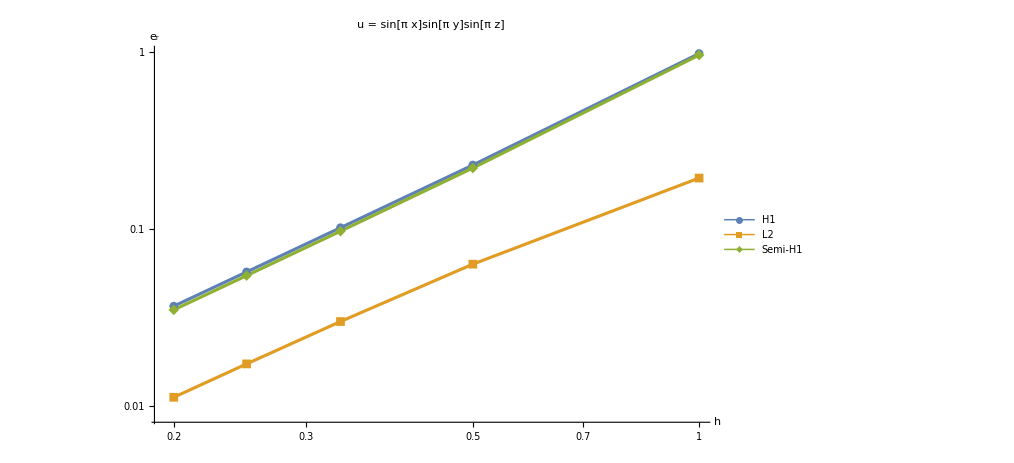

```mathematica
ListLogLogPlot[{ptsh1,ptsl2,ptssemih1},PlotRange->All,PlotStyle->Thickness[0.003],ImageSize->myImageSize 1.5,PlotLabel->Style["u = sin[π x]sin[π y]sin[π z]",14,Black],AxesLabel->{Style["h",myAxesSize,Black],Style["e_r",myAxesSize,Black]},LabelStyle->Directive[myLabelSize,Bold,Black],Joined->True,PlotMarkers->Automatic,PlotLegends->Placed[{"H1","L2","Semi-H1"},{0.55,0.85}]]
```

### Conv rates

```mathematica
convratesh1=Range[Length[neq]-1];
convratesl2=Range[Length[neq]-1];
convratesh1semi=Range[Length[neq]-1];
For[i=1,i≤Length[neq]-1,i++,
convratesh1[[i]]=Log[h1[[i]]/h1[[i+1]]]/Log[h[[i]]/h[[i+1]]];
convratesl2[[i]]=Log[l2[[i]]/l2[[i+1]]]/Log[h[[i]]/h[[i+1]]];
convratesh1semi[[i]]=Log[semih1[[i]]/semih1[[i+1]]]/Log[h[[i]]/h[[i+1]]];
]
convratesh1
convratesl2
convratesh1semi
```

{2.0961,2.0147,2.00394,1.99788}

{1.61924,1.84339,1.91949,1.95077}

{2.12403,2.02978,2.01219,2.00265}